# Exact continuum representation of long-range interacting systems: Example 2: Nonlinear forces in ion chains

by Andreas A. Buchheit and Torsten Keßler

Using the continuum representation, we compute the nonlinear Coulomb forces in a 1D ion chain with a breather (a bound kink-antikink pair).

## Parameters

```mathematica
ClearAll@"Global`*";
```

Interaction exponent (small numerical offset in order to simplify the numerical implementation)

```mathematica
ν1=1+1/1000;
```

Kink width

```mathematica
λ1=5;
```

Kink separation

```mathematica
s1=5;
```

## Breather definition

Position function

```mathematica
r[x_,s_,λ_]=x+1/(Pi)*Integrate[-1/(1+(y-s/2)^2)+1/(1+(y+s/2)^2),{y,-Infinity,x/λ}];
```

## Sum

Interaction potential

```mathematica
V[x_]=x^(-ν);
```

Force sum

```mathematica
ForceSumExact[x_,ν_,s_,λ_]=1/(ν (1+ν))*Sum[(-ν)*(r[x+y,s,λ]-r[x,s,λ])/RealAbs[r[x+y,s,λ]-r[x,s,λ]]^(ν+2),{y,1,200*λ1}]+1/1/(ν (1+ν))*Sum[(-ν)*(r[x+y,s,λ]-r[x,s,λ])/RealAbs[r[x+y,s,λ]-r[x,s,λ]]^(ν+2),{y,-200*λ1,-1}];
```

## Integral

```mathematica
Integral[x_,ν_,s_,λ_,ϵ_]:=1/(ν (1+ν))*Quiet[NIntegrate[(-ν)*(r[x+y,s,λ]-r[x,s,λ])/RealAbs[r[x+y,s,λ]-r[x,s,λ]]^(ν+2),{y,ϵ,200*λ},WorkingPrecision->20]]+1/(ν (1+ν))*Quiet[NIntegrate[(-ν)*(r[x+y,s,λ]-r[x,s,λ])/RealAbs[r[x+y,s,λ]-r[x,s,λ]]^(ν+2),{y,-200*λ,-ϵ},WorkingPrecision->20]];
```

The epsilon correction yields  together with above integral  an approximation to the Hadamard integral.

```mathematica
EpsilonCorrection[x_,ν_,s_,λ_,ϵ_]=1/2*D[r[x,s,λ],{x,2}]/RealAbs[D[r[x,s,λ],x]]^(ν+2)*Integrate[2/y^(ν),{y,ϵ,Infinity}]//Normal;
```

## SEM Operator

```mathematica
SEMCorrection[x_,ν_,s_,λ_]=Zeta[ν]*D[r[x,s,λ],{x,2}]/RealAbs[D[r[x,s,λ],x]]^(ν+2);
```

```mathematica
ForceSEM[x_,ν_,s_,λ_]:=Integral[x,ν,s,λ,1/20]-N[EpsilonCorrection[x,ν,s,λ,1/20],30]+N[SEMCorrection[x,ν,s,λ],30];
```

## Data acquisition

We numerically compute the interaction energy of the test particle via exact summation, the standard integral approximation, and the SEM expansion and compare the results .

```mathematica
tabExact=ParallelTable[{x/λ1,λ1^2*N[ForceSumExact[x,ν1,s1,λ1],15]},{x,-50,50}];
```

```mathematica
tabIntegral=ParallelTable[{x/λ1,λ1^2*N[Integral[x,ν1,s1,λ1,1],15]},{x,-50,50,1/20}];
```

```mathematica
p1=ListPlot[tabExact,AxesLabel->{"x/λ","λ^2 F(x)"},PlotStyle->{PointSize->.015}];
```

```mathematica
p2=ListLinePlot[tabIntegral,PlotStyle->Black,Frame->True,AxesLabel->{"x/λ","λ^2F(x)"}];
```

We find that the integral approximation underestimates the absolute value of the forces and hence yields a result that is qualitatively unreliable.

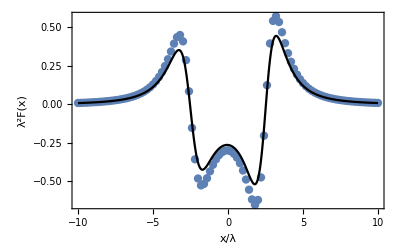

```mathematica
Show[p1,p2,Frame->True,AxesLabel->{"x/λ","λ^2F(x)"},LabelStyle->{FontSize->15}]
```

```mathematica
tabSEM=ParallelTable[{x/λ1,λ1^2*N[ForceSEM[x,ν1,s1,λ1],15]},{x,-50,50,1/20}];
```

```mathematica
p3=ListLinePlot[tabSEM,PlotStyle->Red,AxesLabel->{"x/λ","λ^2F(x)"}];
```

The SEM expansion, on the other hand, precisely reproduces the exact forces.

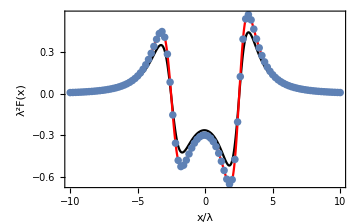

```mathematica
p4=Show[p2,p3,p1,PlotRange->All,ImageSize->Medium,AxesLabel->{"x/λ","λ^2F(x)"},LabelStyle->{FontSize->15}]
```

We now move on to macroscopic lengthscales.

```mathematica
λMacro=10^5;
```

```mathematica
tabIntegralMacro=ParallelTable[{x,λMacro^2*N[Integral[x*λMacro,ν1,s1,λMacro,1],15]},{x,-10,10,1/50}];
```

```mathematica
tabSEMMacro=ParallelTable[{x,λMacro^2*N[ForceSEM[x*λMacro,ν1,s1,λMacro],15]},{x,-10,10,1/50}];
```

```mathematica
p1Macro=ListLinePlot[tabIntegralMacro,PlotStyle->Black];
```

```mathematica
p2Macro=ListLinePlot[tabSEMMacro,PlotStyle->Red];
```

Using our representation, we can compute much larger structures, where exact summation is not available anymore. Here, we find that even in the limit of macroscopic lengths, a noticable difference between the integral approximation and the SEM expansion remains.

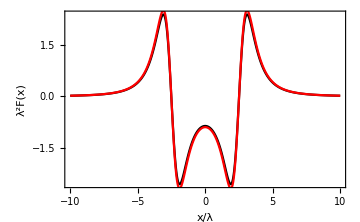

```mathematica
Show[p1Macro,p2Macro,Frame->True,ImageSize->Medium,AxesLabel->{"x/λ","λ^2F(x)"},LabelStyle->{FontSize->15}]
```